## Section | Templates, Icons and Free-form Input

### Completion and Templates

The Input Assistant completes functions and provides function templates:

```mathematica
Plot[f,{x,Subscript[x, min],Subscript[x, max]}]
```

### Iconize

Iconize —from the menu or via a command—can be used to simplify function calls:

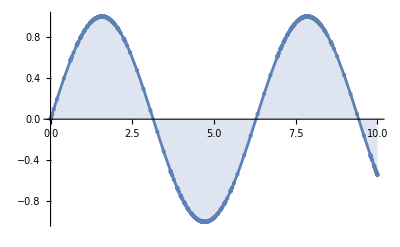

```mathematica
Plot[Sin[x],{x,0,10},]
```

Apply Iconize to a Sequence of options, here named “Options”:

```mathematica
Iconize[Sequence[Filling->Axis,Mesh->All,PlotRange->1/2],"Options"]
```

Copy and paste these iconized options into another Plot command:

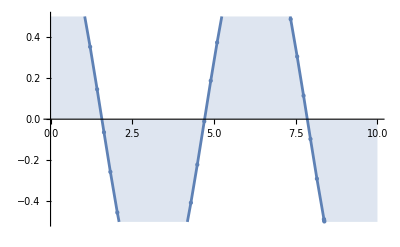

```mathematica
Plot[Cos[x],{x,0,10},]
```

### Free-form Input

You do not have to know precise Wolfram Language syntax to enter computable input. Many expressions can be entered “free-form”, using natural language:

To enter inline free-form input, press ctrl== or invoke the menu command. Type the free-form input, then press  to interpret the input.

Initially, as you are typing, the free-form linguistics interface looks like this: LinguisticAssistant. Once the input is interpreted, the iconography changes to this: LinguisticAssistant

Compute ∫x sin(x)ⅆx:

WolframAlphaQueryParseResults

-x Cos[x]+Sin[x]

Use Evaluate and free-form input inline to compute and then Plot this integral:

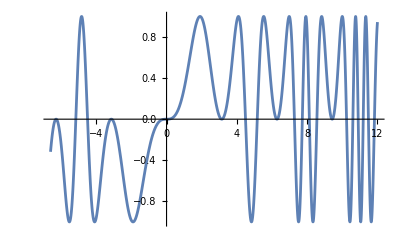

```mathematica
Plot[Evaluate@Sin[LinguisticAssistant], {x, -6.6, 12}]
```

### A Curious Mass Ratio

The following mass ratio involving m_e (electron mass), m_μ (muon mass), and m_τ (tau mass) appears in The 5 Biggest Physics Mysteries on @SabineHossenfelder’s YouTube channel:

(m_e+m_μ+m_τ)/(√m_e+√m_μ+√m_τ)^2≈0.6666617≈2/3

A nice exercise is to check this computation.

#### Direct Computation

Determine the masses or mass-energy equivalences (see the ParticleData Source Information):

```mathematica
m[e]=Entity["Particle","Electron"][EntityProperty["Particle","Mass"]]
```

510.9989461 keV/c^2

```mathematica
m[μ]=Entity["Particle","Muon"][EntityProperty["Particle","Mass"]]
```

105.6583745 MeV/c^2

```mathematica
m[τ]=Entity["Particle","TauLepton"][EntityProperty["Particle","Mass"]]
```

1.77686 GeV/c^2

Note that these outputs include dimensional units as Quantity expressions.

Compute the mass ratio expression:

```mathematica
(m[e]+m[μ]+m[τ])/(√m[e]+√m[μ]+√m[τ])^2
```

0.66666

As expected, this result is dimensionless and is consistent with the quoted value.

#### Uncertainty

The standard uncertainty for these masses can be obtained and gives a better handle on whether the “true” value is 2/3.

Determine the standard uncertainty for the electron mass error:

WolframAlphaQueryParseResults

(0.51099894613333) MeV/c^2

Alternatively, one can use FreeformEvaluate[“query”] or =[query] to interpret query using Wolfram|Alpha and compute the result:

```mathematica
=[electron mass error]
```

(0.51099894613333) MeV/c^2

Using Through and the entity property  yields the mass errors for the three neutrino masses:

```mathematica
{m[e],m[μ],m[τ]}=Through[{Entity["Particle","Electron"],Entity["Particle","Muon"],Entity["Particle","TauLepton"]}[]]
```

{(0.51099894613333) MeV/c^2,(105.65837452525) MeV/c^2,(1776.860.130.13) MeV/c^2}

Use AroundReplace to obtain the uncertainty in the result:

```mathematica
AroundReplace[(Subscript[m, e]+Subscript[m, μ]+Subscript[m, τ])/(√Subscript[m, e]+√Subscript[m, μ]+√Subscript[m, τ])^2,{Subscript[m, e]->m[e],Subscript[m, μ]->m[μ],Subscript[m, τ]->m[τ]}]
```

0.66666177

It looks like 2/3 is not the most probable value for this expression—although it is a possible one.

#### Distribution

Looking at the distribution is instructive.

Use QuantityMagnitude to extract the quantities:

```mathematica
{m[e],m[μ],m[τ]}=QuantityMagnitude[{m[e],m[μ],m[τ]}]
```

{0.51099894613333,105.65837452525,1776.860.130.13}

Assuming that the uncertainty for each of these masses is normally distributed, use TransformedDistribution to determine the uncertainty for the mass ratio:

```mathematica
td=TransformedDistribution[(Subscript[m, e]+Subscript[m, μ]+Subscript[m, τ])/(√Subscript[m, e]+√Subscript[m, μ]+√Subscript[m, τ])^2,{Subscript[m, e]\[Distributed]NormalDistribution[m[e]["Value"],m[e]["Uncertainty"]⟦1⟧],Subscript[m, μ]\[Distributed]NormalDistribution[m[μ]["Value"],m[μ]["Uncertainty"]⟦1⟧],Subscript[m, τ]\[Distributed]NormalDistribution[m[τ]["Value"],m[τ]["Uncertainty"]⟦1⟧]}];
```

Use RandomVariate to simulate the continuous probability distribution and display the result as a Histogram:

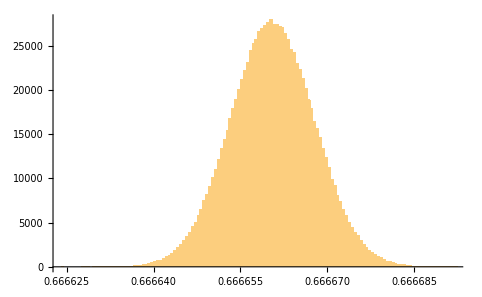

```mathematica
Histogram[RandomVariate[td,10^6],100,GridLines->{{2/3},None},GridLinesStyle->Red]
```

One observes that 2/3 is not the most likely value for this mass ratio.